## Chemistry

```mathematica
caffeine=Entity["Chemical","Caffeine"]
```

caffeine

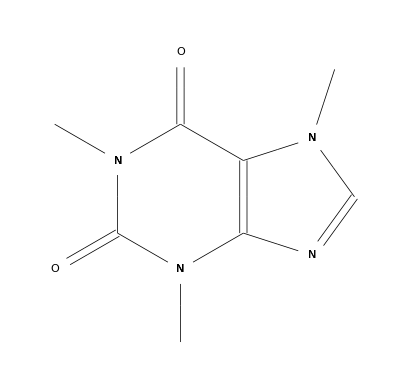

```mathematica
ChemicalData[Entity["Chemical","Caffeine"],"StructureDiagram"]
```

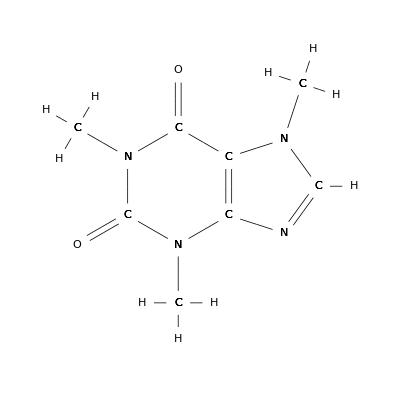

```mathematica
ChemicalData[Entity["Chemical","Caffeine"],"CHStructureDiagram"]
```

```mathematica
ChemicalData[Entity["Chemical","Caffeine"],"MoleculePlot"]
```

-Graphics3D-

```mathematica
MoleculePlot3D[caffeine]
```

-Graphics3D-

```mathematica
planets=EntityClass["Planet",All]
```

planets

```mathematica
EntityList[planets]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

```mathematica
Entity["Planet","Jupiter"]
```

Jupiter

```mathematica
Entity["Planet","Jupiter"]["Satellites"]
```

{Metis,Adrastea,Amalthea,Thebe,Io,Europa,Ganymede,Callisto,Themisto,Leda,S/2018 J1,Himalia,S/2017 J4,Lysithea,Elara,Dia,S/2003 J12,Carpo,Valetudo,Euporie,S/2003 J3,S/2003 J18,S/2017 J7,S/2017 J3,S/2016 J1,Orthosie,Euanthe,Harpalyke,Praxidike,Thyone,S/2003 J16,S/2010 J1,S/2010 J2,Iocaste,Mneme,Hermippe,Thelxinoe,Helike,Ananke,S/2017 J9,S/2017 J6,S/2003 J15,Eurydome,Arche,Herse,Pasithee,S/2003 J10,Chaldene,S/2011 J2,Isonoe,S/2017 J5,S/2017 J8,Erinome,Kale,Aitne,S/2017 J2,Taygete,S/2003 J9,Carme,S/2011 J1,Sponde,Megaclite,S/2003 J5,S/2003 J19,S/2017 J1,S/2003 J23,Kalyke,Kore,Pasiphae,Eukelade,S/2003 J4,Sinope,Hegemone,Aoede,Kallichore,Autonoe,Callirrhoe,Cyllene,S/2003 J2}

```mathematica
PlanetData[Entity["Planet","Jupiter"],"AtmosphericComposition"]
```

<|hydrogen→(85.to87.5)  vol%,helium→(10.to16.3)  vol%,methane→(0.23to0.247)  vol%,ammonia→(0to0.1)  vol%,water→(0.003to0.0099)  vol%,hydrogen sulfide→(0.0002to0.01)  vol%,neon→(0.002to0.00257)  vol%,deuterium hydride→0.0011  vol%,argon→(0.0002to0.0015)  vol%,phosphine→(0to0.001)  vol%,ethane→(0to0.0005)  vol%,ethylene→(0to0.00002)  vol%,methane-d 1→2.×10^-6  vol%,acetylene→(0to3.02×10^-6)  vol%,krypton→(4.×10^-7to1.3×10^-6)  vol%,xenon→(2.×10^-7to8.1×10^-7)  vol%,germane→6.×10^-8  vol%,methylamine→(0to2.×10^-7)  vol%,hydrogen cyanide→(0to2.×10^-7)  vol%,carbon monoxide→1.×10^-8  vol%|>

```mathematica
song=Import["E:\\KuGou\\kanon - 雪之少女.mp3"]
```

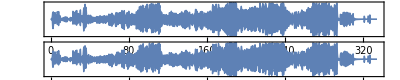

```mathematica
AudioPlot[song]
```

```mathematica
AudioSpectralMap[#Value^1&,song]
```

```mathematica
AudioSpectralTransformation
```

```mathematica
Spectrogram[song]
```

-Graphics-

```mathematica
?Video*
```